```mathematica
NS[]
```

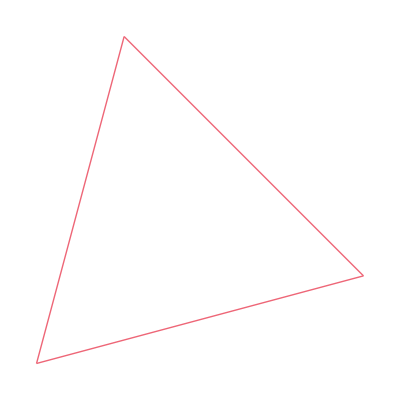

```mathematica
ClearAll[repr];n=2;
Co[x_]:=Flatten@{1-Total@Flatten@x,x};
u=Table[1,n+1];repr[f_]:=IdentityMatrix[{n,n+1}].RotationMatrix[{u,{0,0,1}}].f;
simp=Graphics[Sequence@@{red,Line[#]}&/@T/@(repr/@T/@Subsets[IdentityMatrix[n+1],{2}])]
```

```mathematica
freq[data_]:=(#/Total@#)&@(Count[data,#]&/@Range[3]);
```

```mathematica
ClearAll[f];MF/@(Evaluate[Array[f,3]]=Permutations[{6,1,1}/8])
```

{(3/4
1/8
1/8),(1/8
3/4
1/8),(1/8
1/8
3/4)}

```mathematica
post[data_]:=Block[{tab=Table[Times@@((f[m][[#]])&/@data),{m,3}]},tab/Total[tab]]
```

```mathematica
pred[data_]:=post[data].T[Array[f,3]]
```

```mathematica
SeedRandom[999];ft={2,1,1}.Array[f,3]/4;data=RandomChoice[ft->Range[3],15]
```

{1,3,1,1,1,3,1,2,3,2,3,2,3,2,1}

```mathematica
{ft,(fe=freq[data])}//N
```

{{0.4375,0.28125,0.28125},{0.4,0.266667,0.333333}}

```mathematica
MF/@(seqpost=Table[post[data[[;;t]]],{t,Length@data}])//N
```

{(0.75
0.125
0.125),(0.461538
0.0769231
0.461538),(0.837209
0.0232558
0.139535),(0.96861
0.0044843
0.0269058),(0.994628
0.00076746
0.00460476),(0.972243
0.000750188
0.0270068),(0.995264
0.000127992
0.00460771),(0.994628
0.00076746
0.00460476),(0.972243
0.000750188
0.0270068),(0.96861
0.0044843
0.0269058),(0.853755
0.00395257
0.142292),(0.837209
0.0232558
0.139535),(0.493151
0.0136986
0.493151),(0.461538
0.0769231
0.461538),(0.837209
0.0232558
0.139535)}

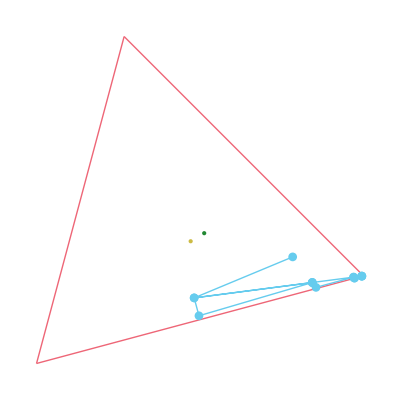

```mathematica
seqpostp=ListPlot[repr/@seqpost,Joined->True,PlotRange->All,PlotMarkers->Auto];
Show[{simp,seqpostp,Graphics[{green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}]
```

```mathematica
Animate[Show[{simp,Graphics[{Black,Text[t,repr@seqpost[[t]]],yellow,Opacity[0.5],PointSize[Large],Point[repr@seqpost[[t]]],green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}],{t,1,Length@data,1}]
```

```mathematica
(MF/@(seqpred=Table[pred[data[[;;t]]],{t,Length@data}]))//N
```

{(0.59375
0.203125
0.203125),(0.413462
0.173077
0.413462),(0.648256
0.139535
0.212209),(0.730381
0.127803
0.141816),(0.746642
0.12548
0.127878),(0.732652
0.125469
0.141879),(0.74704
0.12508
0.12788),(0.746642
0.12548
0.127878),(0.732652
0.125469
0.141879),(0.730381
0.127803
0.141816),(0.658597
0.12747
0.213933),(0.648256
0.139535
0.212209),(0.433219
0.133562
0.433219),(0.413462
0.173077
0.413462),(0.648256
0.139535
0.212209)}

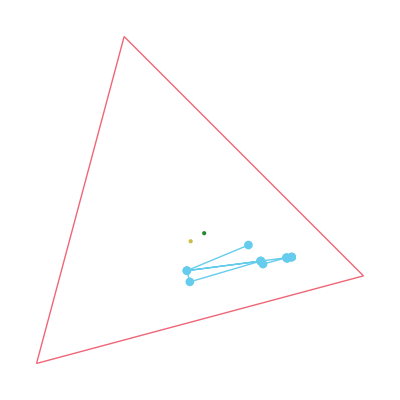

```mathematica
seqpredp=ListPlot[repr/@seqpred,Joined->True,PlotRange->All,PlotMarkers->Auto];
Show[{simp,seqpredp,Graphics[{green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}]
```

```mathematica
Animate[Show[{simp,Graphics[{Black,Text[t,repr@seqpred[[t]]],yellow,Opacity[0.5],PointSize[Large],Point[repr@seqpred[[t]]],green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}],{t,1,Length@data,1}]
```